```mathematica
A=Integrate[x*Sin[(π*r*x)/l],{x,0,l/2}]
```

(l (-1/2 l π r Cos[(π r)/2]+l Sin[(π r)/2]))/(π^2 r^2)

```mathematica
B=Integrate[(l-x)*Sin[(π*r*x)/l],{x,l/2,l}]
```

(l^2 (π r Cos[(π r)/2]+2 Sin[(π r)/2]-2 Sin[π r]))/(2 π^2 r^2)

```mathematica
A+B
```

(l (-1/2 l π r Cos[(π r)/2]+l Sin[(π r)/2]))/(π^2 r^2)+(l^2 (π r Cos[(π r)/2]+2 Sin[(π r)/2]-2 Sin[π r]))/(2 π^2 r^2)

```mathematica
Simplify[(l (-1/2 l π r Cos[(π r)/2]+l Sin[(π r)/2]))/(π^2 r^2)+(l^2 (π r Cos[(π r)/2]+2 Sin[(π r)/2]-2 Sin[π r]))/(2 π^2 r^2)]
```

(8 l^2 Cos[(π r)/4] Sin[(π r)/4]^3)/(π^2 r^2)

```mathematica
T=A+B
```

(l (-1/2 l π r Cos[(π r)/2]+l Sin[(π r)/2]))/(π^2 r^2)+(l^2 (π r Cos[(π r)/2]+2 Sin[(π r)/2]-2 Sin[π r]))/(2 π^2 r^2)

```mathematica
T
```

(l (-1/2 l π r Cos[(π r)/2]+l Sin[(π r)/2]))/(π^2 r^2)+(l^2 (π r Cos[(π r)/2]+2 Sin[(π r)/2]-2 Sin[π r]))/(2 π^2 r^2)

```mathematica
Simplify[(l (-1/2 l π r Cos[(π r)/2]+l Sin[(π r)/2]))/(π^2 r^2)+(l^2 (π r Cos[(π r)/2]+2 Sin[(π r)/2]-2 Sin[π r]))/(2 π^2 r^2)]
```

(8 l^2 Cos[(π r)/4] Sin[(π r)/4]^3)/(π^2 r^2)

```mathematica
T=Simplify[T]
```

```mathematica
(8 l^2 Cos[(π r)/4] Sin[(π r)/4]^3)/(π^2 r^2)
T=T*(4*h)/l^2
```

(8 l^2 Cos[(π r)/4] Sin[(π r)/4]^3)/(π^2 r^2)

(32 h Cos[(π r)/4] Sin[(π r)/4]^3)/(π^2 r^2)

```mathematica
Sum[T*Sin[(π*r*x)/l]*Cos[(π*r*c)/l*t],{r,1,5}]
```

(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)

```mathematica
Animate[Plot[(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)/.{h->1,l->2,c->2},{x,0,2},PlotRange->{{0,2},{-1,1}}],{t,0,10}]
```

```mathematica
Simplify[(l (-1/2 l π r Cos[(π r)/2]+l Sin[(π r)/2]))/(π^2 r^2)+(l^2 (π r Cos[(π r)/2]+2 Sin[(π r)/2]))/(2 π^2 r^2)]
```

(2 l^2 Sin[(π r)/2])/(π^2 r^2)

```mathematica
T=4*h/l^2*(2 l^2 Sin[(π r)/2])/(π^2 r^2)
```

(8 h Sin[(π r)/2])/(π^2 r^2)

```mathematica
Sum[T*Sin[(π*r*x)/l]*Cos[(π*r*c)/l*t],{r,1,5}]
```

(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)

```mathematica
Animate[Plot[(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)/.{h->1,l->2,c->0.5},{x,0,2},PlotRange->{{0,2},{-1,1}}],{t,0,10}]
```

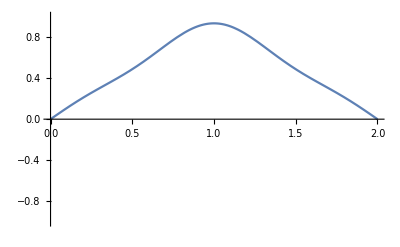

```mathematica
Plot[(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)/.{h->1,l->2,c->0.5,t->0},{x,0,2},PlotRange->{{0,2},{-1,1}}]
```

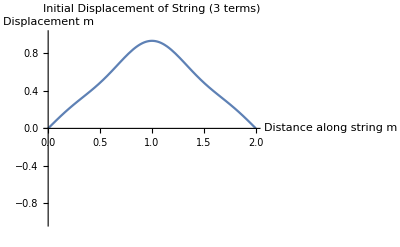

```mathematica
Show[%9,AxesLabel->{HoldForm[Distance along string m],HoldForm[Displacement m]},PlotLabel->HoldForm[Initial Displacement of String (3 terms)],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Sum[T*Sin[(π*r*x)/l]*Cos[(π*r*c)/l*t],{r,1,20}]
```

(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)-(8 h Cos[(7 c π t)/l] Sin[(7 π x)/l])/(49 π^2)+(8 h Cos[(9 c π t)/l] Sin[(9 π x)/l])/(81 π^2)-(8 h Cos[(11 c π t)/l] Sin[(11 π x)/l])/(121 π^2)+(8 h Cos[(13 c π t)/l] Sin[(13 π x)/l])/(169 π^2)-(8 h Cos[(15 c π t)/l] Sin[(15 π x)/l])/(225 π^2)+(8 h Cos[(17 c π t)/l] Sin[(17 π x)/l])/(289 π^2)-(8 h Cos[(19 c π t)/l] Sin[(19 π x)/l])/(361 π^2)

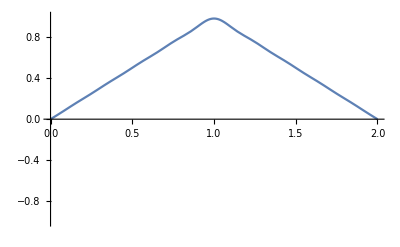

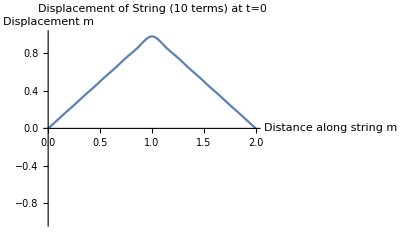

```mathematica
Plot[(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)-(8 h Cos[(7 c π t)/l] Sin[(7 π x)/l])/(49 π^2)+(8 h Cos[(9 c π t)/l] Sin[(9 π x)/l])/(81 π^2)-(8 h Cos[(11 c π t)/l] Sin[(11 π x)/l])/(121 π^2)+(8 h Cos[(13 c π t)/l] Sin[(13 π x)/l])/(169 π^2)-(8 h Cos[(15 c π t)/l] Sin[(15 π x)/l])/(225 π^2)+(8 h Cos[(17 c π t)/l] Sin[(17 π x)/l])/(289 π^2)-(8 h Cos[(19 c π t)/l] Sin[(19 π x)/l])/(361 π^2)/.{h->1,l->2,c->0.5,t->0},{x,0,2},PlotRange->{{0,2},{-1,1}}]
Show[%18,AxesLabel->{HoldForm[Distance along string m],HoldForm[Displacement m]},PlotLabel->HoldForm[Displacement of String (10 terms) at t=0],LabelStyle->{GrayLevel[0]}]
```

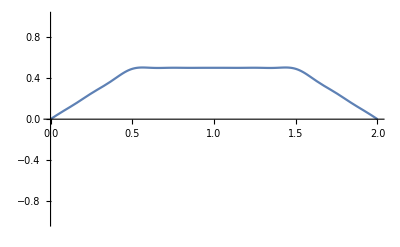

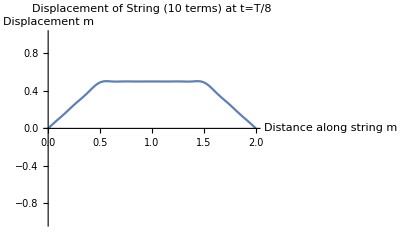

```mathematica
Plot[(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)-(8 h Cos[(7 c π t)/l] Sin[(7 π x)/l])/(49 π^2)+(8 h Cos[(9 c π t)/l] Sin[(9 π x)/l])/(81 π^2)-(8 h Cos[(11 c π t)/l] Sin[(11 π x)/l])/(121 π^2)+(8 h Cos[(13 c π t)/l] Sin[(13 π x)/l])/(169 π^2)-(8 h Cos[(15 c π t)/l] Sin[(15 π x)/l])/(225 π^2)+(8 h Cos[(17 c π t)/l] Sin[(17 π x)/l])/(289 π^2)-(8 h Cos[(19 c π t)/l] Sin[(19 π x)/l])/(361 π^2)/.{h->1,l->2,c->0.5,t->1/8*8},{x,0,2},PlotRange->{{0,2},{-1,1}}]
Show[%40,AxesLabel->{HoldForm[Distance along string m],HoldForm[Displacement m]},PlotLabel->HoldForm[Displacement of String (10 terms) at t=T/8],LabelStyle->{GrayLevel[0]}]
```

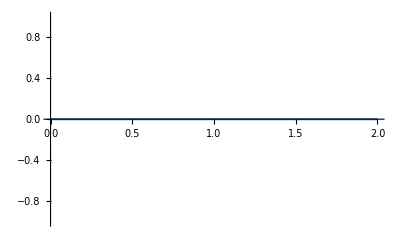

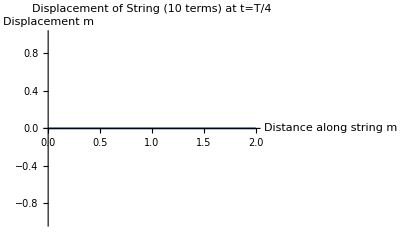

```mathematica
Plot[(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)-(8 h Cos[(7 c π t)/l] Sin[(7 π x)/l])/(49 π^2)+(8 h Cos[(9 c π t)/l] Sin[(9 π x)/l])/(81 π^2)-(8 h Cos[(11 c π t)/l] Sin[(11 π x)/l])/(121 π^2)+(8 h Cos[(13 c π t)/l] Sin[(13 π x)/l])/(169 π^2)-(8 h Cos[(15 c π t)/l] Sin[(15 π x)/l])/(225 π^2)+(8 h Cos[(17 c π t)/l] Sin[(17 π x)/l])/(289 π^2)-(8 h Cos[(19 c π t)/l] Sin[(19 π x)/l])/(361 π^2)/.{h->1,l->2,c->0.5,t->2/8*8},{x,0,2},PlotRange->{{0,2},{-1,1}}]
Show[%44,AxesLabel->{HoldForm[Distance along string m],HoldForm[Displacement m]},PlotLabel->HoldForm[Displacement of String (10 terms) at t=T/4],LabelStyle->{GrayLevel[0]}]
```

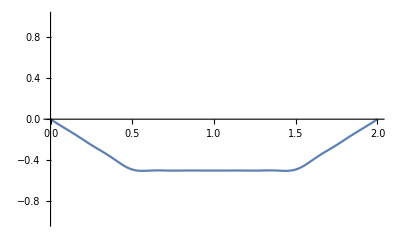

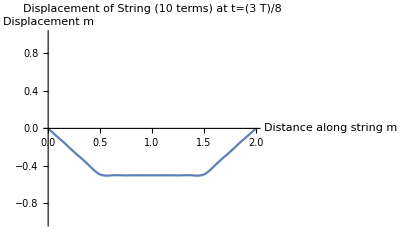

```mathematica
Plot[(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)-(8 h Cos[(7 c π t)/l] Sin[(7 π x)/l])/(49 π^2)+(8 h Cos[(9 c π t)/l] Sin[(9 π x)/l])/(81 π^2)-(8 h Cos[(11 c π t)/l] Sin[(11 π x)/l])/(121 π^2)+(8 h Cos[(13 c π t)/l] Sin[(13 π x)/l])/(169 π^2)-(8 h Cos[(15 c π t)/l] Sin[(15 π x)/l])/(225 π^2)+(8 h Cos[(17 c π t)/l] Sin[(17 π x)/l])/(289 π^2)-(8 h Cos[(19 c π t)/l] Sin[(19 π x)/l])/(361 π^2)/.{h->1,l->2,c->0.5,t->3/8*8},{x,0,2},PlotRange->{{0,2},{-1,1}}]
Show[%46,AxesLabel->{HoldForm[Distance along string m],HoldForm[Displacement m]},PlotLabel->HoldForm[Displacement of String (10 terms) at t=3*T/8],LabelStyle->{GrayLevel[0]}]
```

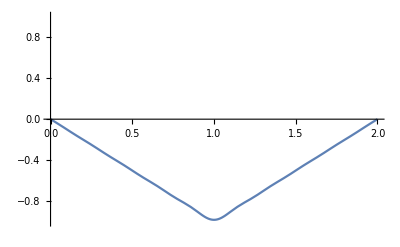

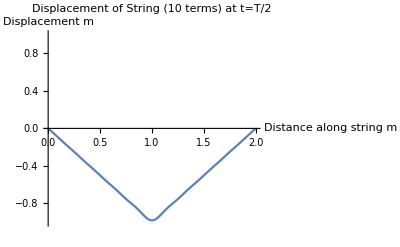

```mathematica
Plot[(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)-(8 h Cos[(7 c π t)/l] Sin[(7 π x)/l])/(49 π^2)+(8 h Cos[(9 c π t)/l] Sin[(9 π x)/l])/(81 π^2)-(8 h Cos[(11 c π t)/l] Sin[(11 π x)/l])/(121 π^2)+(8 h Cos[(13 c π t)/l] Sin[(13 π x)/l])/(169 π^2)-(8 h Cos[(15 c π t)/l] Sin[(15 π x)/l])/(225 π^2)+(8 h Cos[(17 c π t)/l] Sin[(17 π x)/l])/(289 π^2)-(8 h Cos[(19 c π t)/l] Sin[(19 π x)/l])/(361 π^2)/.{h->1,l->2,c->0.5,t->4/8*8},{x,0,2},PlotRange->{{0,2},{-1,1}}]
Show[%48,AxesLabel->{HoldForm[Distance along string m],HoldForm[Displacement m]},PlotLabel->HoldForm[Displacement of String (10 terms) at t=T/2],LabelStyle->{GrayLevel[0]}]
```

-Graphics-

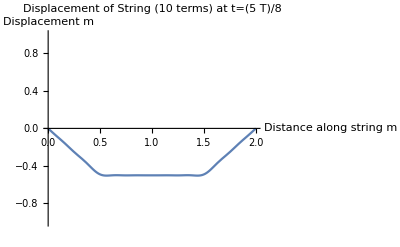

```mathematica
Plot[(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)-(8 h Cos[(7 c π t)/l] Sin[(7 π x)/l])/(49 π^2)+(8 h Cos[(9 c π t)/l] Sin[(9 π x)/l])/(81 π^2)-(8 h Cos[(11 c π t)/l] Sin[(11 π x)/l])/(121 π^2)+(8 h Cos[(13 c π t)/l] Sin[(13 π x)/l])/(169 π^2)-(8 h Cos[(15 c π t)/l] Sin[(15 π x)/l])/(225 π^2)+(8 h Cos[(17 c π t)/l] Sin[(17 π x)/l])/(289 π^2)-(8 h Cos[(19 c π t)/l] Sin[(19 π x)/l])/(361 π^2)/.{h->1,l->2,c->0.5,t->5/8*8},{x,0,2},PlotRange->{{0,2},{-1,1}}]
Show[%50,AxesLabel->{HoldForm[Distance along string m],HoldForm[Displacement m]},PlotLabel->HoldForm[Displacement of String (10 terms) at t=5*T/8],LabelStyle->{GrayLevel[0]}]
```

-Graphics-

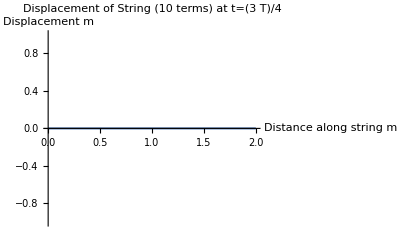

```mathematica
Plot[(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)-(8 h Cos[(7 c π t)/l] Sin[(7 π x)/l])/(49 π^2)+(8 h Cos[(9 c π t)/l] Sin[(9 π x)/l])/(81 π^2)-(8 h Cos[(11 c π t)/l] Sin[(11 π x)/l])/(121 π^2)+(8 h Cos[(13 c π t)/l] Sin[(13 π x)/l])/(169 π^2)-(8 h Cos[(15 c π t)/l] Sin[(15 π x)/l])/(225 π^2)+(8 h Cos[(17 c π t)/l] Sin[(17 π x)/l])/(289 π^2)-(8 h Cos[(19 c π t)/l] Sin[(19 π x)/l])/(361 π^2)/.{h->1,l->2,c->0.5,t->6/8*8},{x,0,2},PlotRange->{{0,2},{-1,1}}]
Show[%52,AxesLabel->{HoldForm[Distance along string m],HoldForm[Displacement m]},PlotLabel->HoldForm[Displacement of String (10 terms) at t=3*T/4],LabelStyle->{GrayLevel[0]}]
```

-Graphics-

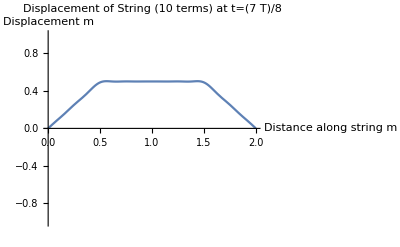

```mathematica
Plot[(8 h Cos[(c π t)/l] Sin[(π x)/l])/π^2-(8 h Cos[(3 c π t)/l] Sin[(3 π x)/l])/(9 π^2)+(8 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(25 π^2)-(8 h Cos[(7 c π t)/l] Sin[(7 π x)/l])/(49 π^2)+(8 h Cos[(9 c π t)/l] Sin[(9 π x)/l])/(81 π^2)-(8 h Cos[(11 c π t)/l] Sin[(11 π x)/l])/(121 π^2)+(8 h Cos[(13 c π t)/l] Sin[(13 π x)/l])/(169 π^2)-(8 h Cos[(15 c π t)/l] Sin[(15 π x)/l])/(225 π^2)+(8 h Cos[(17 c π t)/l] Sin[(17 π x)/l])/(289 π^2)-(8 h Cos[(19 c π t)/l] Sin[(19 π x)/l])/(361 π^2)/.{h->1,l->2,c->0.5,t->7/8*8},{x,0,2},PlotRange->{{0,2},{-1,1}}]
Show[%54,AxesLabel->{HoldForm[Distance along string m],HoldForm[Displacement m]},PlotLabel->HoldForm[Displacement of String (10 terms) at t=7*T/8],LabelStyle->{GrayLevel[0]}]
```

```mathematica
A=Integrate[x*Sin[(π*r*x)/l],{x,0,l/3}]+1/2*Integrate[(l-x)*Sin[(π*r*x)/l],{x,l/3,l}]
```

```mathematica
(l (-1/3 l π r Cos[(π r)/3]+l Sin[(π r)/3]))/(π^2 r^2)+(l^2 (2 π r Cos[(π r)/3]+3 Sin[(π r)/3]))/(6 π^2 r^2)
```

```mathematica
B=Simplify[(l (-1/3 l π r Cos[(π r)/3]+l Sin[(π r)/3]))/(π^2 r^2)+(l^2 (2 π r Cos[(π r)/3]+3 Sin[(π r)/3]))/(6 π^2 r^2)]
```

(3 l^2 Sin[(π r)/3])/(2 π^2 r^2)

```mathematica
T=6*h/l^2*B
```

(9 h Sin[(π r)/3])/(π^2 r^2)

```mathematica
(12 h Sin[(π r)/3]^3)/(π^2 r^2)
```

(12 h Sin[(π r)/3]^3)/(π^2 r^2)

```mathematica
Sum[T*Sin[(π*r*x)/l]*Cos[(π*r*c)/l*t],{r,1,15}]
```

(9 √3 h Cos[(c π t)/l] Sin[(π x)/l])/(2 π^2)+(9 √3 h Cos[(2 c π t)/l] Sin[(2 π x)/l])/(8 π^2)-(9 √3 h Cos[(4 c π t)/l] Sin[(4 π x)/l])/(32 π^2)-(9 √3 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(50 π^2)+(9 √3 h Cos[(7 c π t)/l] Sin[(7 π x)/l])/(98 π^2)+(9 √3 h Cos[(8 c π t)/l] Sin[(8 π x)/l])/(128 π^2)-(9 √3 h Cos[(10 c π t)/l] Sin[(10 π x)/l])/(200 π^2)-(9 √3 h Cos[(11 c π t)/l] Sin[(11 π x)/l])/(242 π^2)+(9 √3 h Cos[(13 c π t)/l] Sin[(13 π x)/l])/(338 π^2)+(9 √3 h Cos[(14 c π t)/l] Sin[(14 π x)/l])/(392 π^2)

```mathematica
Animate[Plot[(9 √3 h Cos[(c π t)/l] Sin[(π x)/l])/(2 π^2)+(9 √3 h Cos[(2 c π t)/l] Sin[(2 π x)/l])/(8 π^2)-(9 √3 h Cos[(4 c π t)/l] Sin[(4 π x)/l])/(32 π^2)-(9 √3 h Cos[(5 c π t)/l] Sin[(5 π x)/l])/(50 π^2)+(9 √3 h Cos[(7 c π t)/l] Sin[(7 π x)/l])/(98 π^2)+(9 √3 h Cos[(8 c π t)/l] Sin[(8 π x)/l])/(128 π^2)-(9 √3 h Cos[(10 c π t)/l] Sin[(10 π x)/l])/(200 π^2)-(9 √3 h Cos[(11 c π t)/l] Sin[(11 π x)/l])/(242 π^2)+(9 √3 h Cos[(13 c π t)/l] Sin[(13 π x)/l])/(338 π^2)+(9 √3 h Cos[(14 c π t)/l] Sin[(14 π x)/l])/(392 π^2)/.{h->1,l->2,c->2},{x,0,2},PlotRange->{{0,2},{-1,1}}],{t,0,10}]
```